# RandomMixedGraph

Change an undirected graph into a mixed graph

## Definition

```mathematica
ClearAll[RandomMixedGraph]
RandomMixedGraph[{vertices_,edges_},threshold_]:=Block[{replaceCount,randomGraph} ,randomGraph=RandomGraph[{vertices,edges}];replaceCount=Floor[threshold edges];Graph[Fold[EdgeAdd[EdgeDelete[#1,#2],First[#2]->Last[#2]]&,randomGraph,RandomSample[EdgeList[randomGraph],replaceCount]],EdgeWeight->Thread[EdgeList[randomGraph]->(AnnotationValue[{randomGraph,#1},EdgeWeight])&/@EdgeList[randomGraph]]]]/;0<=threshold<=1
RandomMixedGraph[{vertices_,edges_},threshold_,k_]:=Block[{replaceCount,randomGraphList} ,randomGraphList=RandomGraph[{vertices,edges},k];replaceCount=Floor[threshold edges];(randomGraph↦Graph[Fold[EdgeAdd[EdgeDelete[#1,#2],First[#2]->Last[#2]]&,randomGraph,RandomSample[EdgeList[randomGraph],replaceCount]],EdgeWeight->Thread[EdgeList[randomGraph]->(AnnotationValue[{randomGraph,#1},EdgeWeight])&/@EdgeList[randomGraph]]])/@randomGraphList]/;0<=threshold<=1
RandomMixedGraph[graphDistribution_,threshold_]:=Block[{replaceCount,randomGraph} ,randomGraph=RandomGraph[graphDistribution];replaceCount=Floor[threshold EdgeCount[randomGraph]];Graph[Fold[EdgeAdd[EdgeDelete[#1,#2],First[#2]->Last[#2]]&,randomGraph,RandomSample[EdgeList[randomGraph],replaceCount]],EdgeWeight->Thread[EdgeList[randomGraph]->(AnnotationValue[{randomGraph,#1},EdgeWeight])&/@EdgeList[randomGraph]]]]/;0<=threshold<=1
```

## Documentation

### Usage

RandomMixedGraph[{n,m},frac]

creates a random graph with n nodes/vertices and m edges with frac of directed edges/arcs.

### Details & Options

A mixed graph is one with both directed and undirected edges. RandomMixedGraph produces a mixed graph by making a random graph and converting a fraction of undirected edges into directed edges.

The input frac should be a number between 0 and 1 that determines the fraction of undirected edges which are coverted to directed edges. A frac value of 0 returns the original graph. A frac value of 1 produces a fully-directed graph (with randomly-oriented edges). A frac value of 0.5 would make approximately 50% of the edges directed.

## Examples

### Basic Examples

Make a random mixed graph with 20 nodes and 48 edges with 75% of the edges directed:

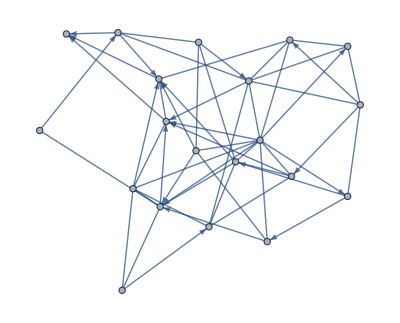

```mathematica
RandomMixedGraph[{20,54},.75]
```

Construct a graph with 5% directed edges:

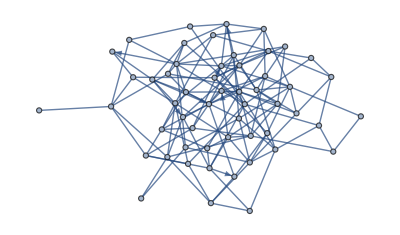

```mathematica
RandomMixedGraph[{54,148},0.05]
```

Make a list of random mixed graphs:

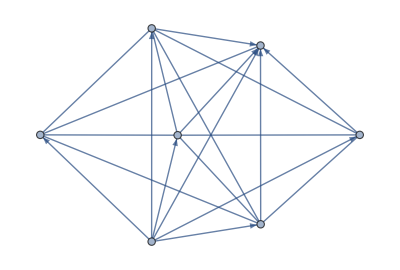
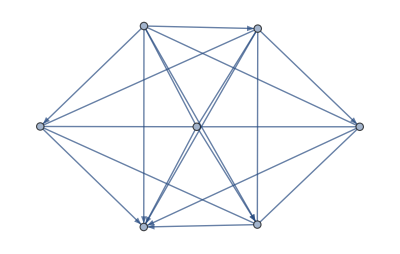
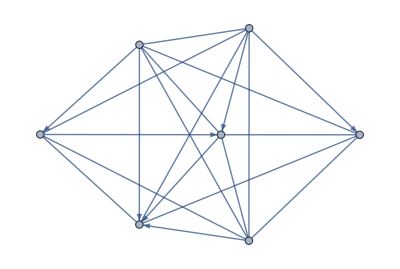

```mathematica
RandomMixedGraph[{7,20},2/3,3]
```

Generate a random spatial graph with 148 nodes and 2/3 directed edges:

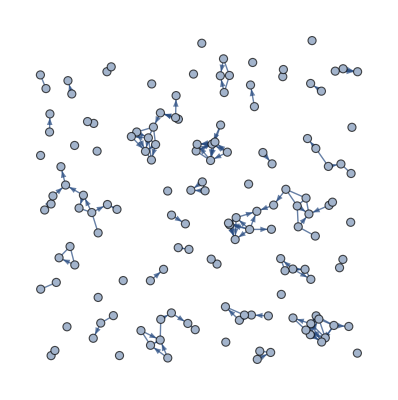

```mathematica
𝒢=RandomMixedGraph[SpatialGraphDistribution[148,0.07],2/3]
```

### Applications

Make a big mixed graph:

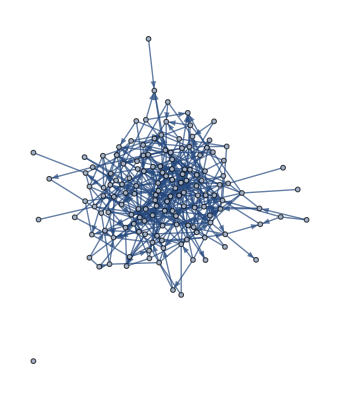

```mathematica
RandomMixedGraph[{148,403},2/3]
```

Verify the output of the function produces a mixed graph:

```mathematica
MixedGraphQ[RandomMixedGraph[{148,403},.75]]
```

True

Evaluate if a mixed graph has a Hamiltonian cycle:

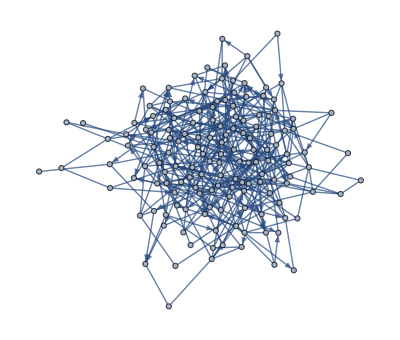

```mathematica
𝒢=RandomMixedGraph[{148,403},ⅇ^-1]
```

```mathematica
HamiltonianGraphQ[𝒢]
```

False

Find the graph union of two mixed graphs:

```mathematica
GraphUnion@@Table[RandomMixedGraph[{20,54},.75],3]
```

-Graphics-

Make an indexed mixed graph:

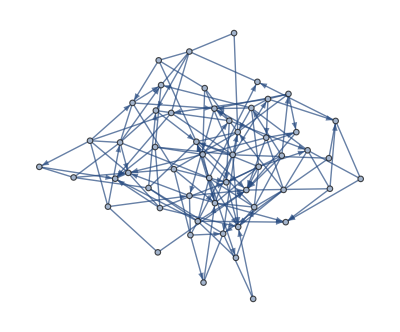

```mathematica
IndexGraph[RandomMixedGraph[{54,148},.75]]
```

Reverse a mixed graph's directed edges:

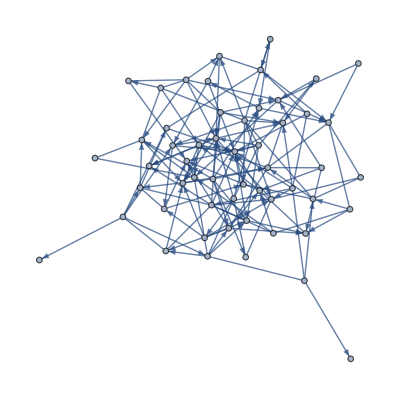

```mathematica
ReverseGraph[RandomMixedGraph[{54,148},.7]]
```

Compute the graph product for various definitions for two mixed graphs:

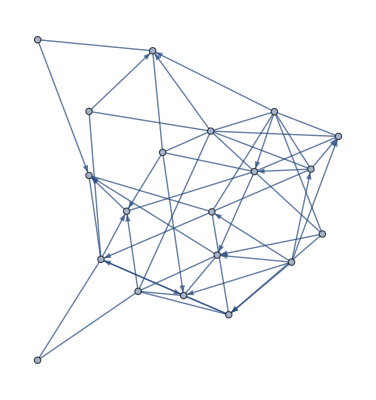

```mathematica
𝒢=RandomMixedGraph[{20,54},.77]
```

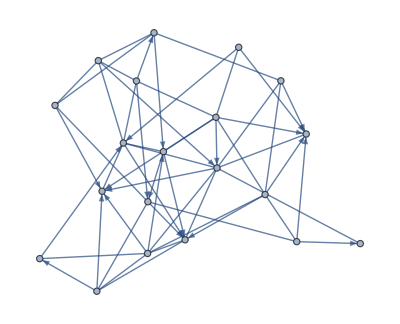

```mathematica
ℋ=RandomMixedGraph[{20,54},.77]
```

```mathematica
Table[GraphProduct[𝒢,ℋ, op, 
  PlotLabel -> Style[op, 8]], {op, {"Cartesian", "Conormal", 
   "Lexicographical", "Normal", "Rooted", "Tensor"}}]
```

-Graphics-

Apply binary graph operations to two small mixed graphs:

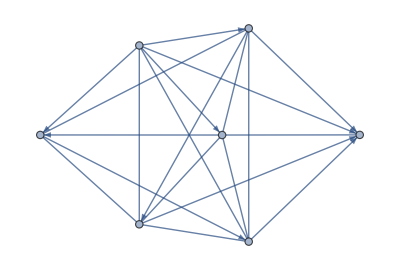

```mathematica
𝒢=RandomMixedGraph[{7,20},.77]
```

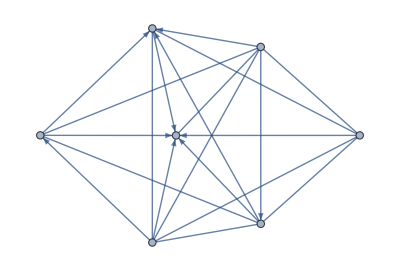

```mathematica
ℋ=RandomMixedGraph[{7,20},.77]
```

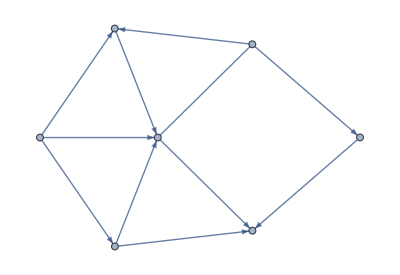
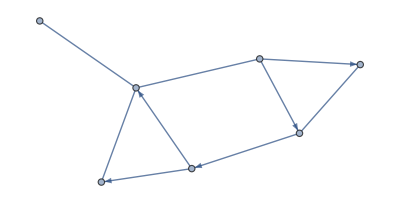
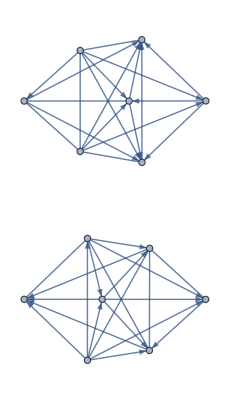
<|(BooleanGraph[Xor,##1]&)→-Graphics-,(BooleanGraph[Nand,##1]&)→-Graphics-,GraphIntersection→-Graphics-,GraphUnion→-Graphics-,GraphDifference→-Graphics-,GraphDisjointUnion→-Graphics-,GraphProduct→-Graphics-,GraphJoin→-Graphics-,GraphSum→-Graphics-|>

```mathematica
AssociationMap[(graphOperation↦graphOperation[𝒢,ℋ]),{BooleanGraph[Xor,##]&,BooleanGraph[Nand,##]&,GraphIntersection,GraphUnion,GraphDifference,GraphDisjointUnion,GraphProduct,GraphJoin,GraphSum}]
```

Evaluate the graph product definitions:

```mathematica
AssociationMap[(graphProduct↦GraphProduct[𝒢,ℋ,graphProduct]),{"Cartesian","Conormal","Lexicographical","Normal","Rooted","Tensor"}]
```

-Graphics-

Compute unary graph operations on a large random mixed graph:

```mathematica
AssociationMap[(graphOperation↦graphOperation[𝒢]),{GraphPower[##,2]&,GraphComplement}]
```

<|(GraphPower[##1,2]&)→-Graphics-,GraphComplement→-Graphics-|>

## Source & Additional Information

### Contributed By

Peter Burbery

### Keywords

graph

directed graph

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

RandomGraph

SpatialGraphDistribution

### Related Resource Objects

OrientedGraphQ

TransitiveGraphQ

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.